## 目的简介

大作业终极目标：用Mathematica实现Mathematica
(所需知识来自符号计算软件与编译原理课程)
基本步骤：
1、词法分析得到一列符号（为一个列表）
2、语法分析得到语法树（在Mathematica中为嵌套的列表）
3、遍历语法树并执行
为了靠近函数式编程的效果，遍历执行并未引入过多中间变量，而是主要通过一个保存变量值与当前结果的查找表构造。
最终效果：一个可以支持大部分变量/函数定义与操作的Mathematica解释器。

## 词法分析

本部分工作：分析输入程序的词法，最终返回分词形成的列表

终结符：
ID 标识符
_下划线
NUM 数字
, 逗号
[[ ]] [ ] ( ) { } 括号
:=  =赋值运算符
>=  <=  ==  !=  >  < 比较运算符
^ 指数运算符
*  / 乘性运算符
+  - 加性运算符
ϵ 空

此部分解决的语法处理：
a+=b一类语句会被替换为a=a+b
通过括号匹配确定连续的右括号哪些为]哪些为]]
自动添加数字字母间的乘号

```mathematica
CMPOP={">=","<=","!=","==",">","<"};
ADDOP={"+","-"};
MULOP={"*","/"};
LBRAC={"(","[","{","[["};
RBRAC={")","]","}","]]"};
```

```mathematica
SplitByLex[program_]:=StringCases[program,RegularExpression["\\d+\\.\\d+|\\d+|[a-zA-Z]\\w*"]|\
"+="|"+"|"-="|"-"|"*="|"*"|"/="|"/"|"^"|"_"|">="|"<="|"!="|"=="|">"|"<"|":="|"="|"{"|"}"|"[["|"["|"]"|"("|")"|","|";"];
```

```mathematica
PreProcessBrackets[sentencelist_]:=Module[{stack,copiedlist,i},copiedlist=sentencelist;stack={};
For[i=1,i≤Length[sentencelist],i++,
If[StringMatchQ[copiedlist[[i]],RegularExpression@"\\d+\\.\\d+|\\d+"],copiedlist[[i]]="0"<>copiedlist[[i]],
If[StringMatchQ[copiedlist[[i]],RegularExpression@"[a-zA-Z]\\w*"],
copiedlist[[i]]=If[StringQ[copiedlist[[i-1]]]&&StringTake[copiedlist[[i-1]],1]=="0",{"*","#"<>copiedlist[[i]]},"#"<>copiedlist[[i]]],
Switch[copiedlist[[i]],
"[",stack=Insert[stack,1,-1],
"[[",stack=Insert[stack,0,-1],
"]",If[stack[[-1]]==1,stack=Delete[stack,-1],stack=Delete[stack,-1];copiedlist[[i]]="]]";copiedlist[[i+1]]={};],
"_",copiedlist[[i-1]]="_"<>StringDrop[copiedlist[[i-1]],1];copiedlist[[i]]={},
"-",If[i==1||MemberQ[Flatten[{LBRAC,",",";"}],copiedlist[[i-1]]],copiedlist[[i]]={"0","-"}]
]]]];
Flatten[copiedlist]];
```

```mathematica
FindLval[sentencelist_,i_]:=Module[{count,j},count=0;j=i;
While[j≥1&&count≥0&&(count≠0||(sentencelist[[j]]≠","&&sentencelist[[j]]≠";")),
If[MemberQ[RBRAC,sentencelist[[j]]],count++,If[MemberQ[LBRAC,sentencelist[[j]]],count--;]];j--];
If[count==-1,j++,If[j==0,j--]];
Take[sentencelist,{j+1,i-1}]];
```

```mathematica
PreProcessAssign[sentencelist_]:=Module[{copiedlist,i},copiedlist=sentencelist;For[i=1,i≤Length[sentencelist],i++,
Switch[copiedlist[[i]],"+=",copiedlist[[i]]={"=",FindLval[sentencelist,i],"+"},
"-=",copiedlist[[i]]={"=",FindLval[sentencelist,i],"-"},
"*=",copiedlist[[i]]={"=",FindLval[sentencelist,i],"*"},
"/=",copiedlist[[i]]={"=",FindLval[sentencelist,i],"/"}]];Flatten[copiedlist]];
```

```mathematica
LEX[program_]:=PreProcessAssign@PreProcessBrackets@SplitByLex@program;
```

## 语法分析

本部分工作：将词法的线性列表转化为语法树，从而可以执行

上下文无关文法：
program -> sentences
sentences -> sentences sentence | sentence
sentence -> var-assign | func-assign | expression
var-assign -> var = expression
var -> ID | ID layer
layer -> layer [[expression]] | [[expression]]
func-assign -> ID[param-list] := expression
param-list -> param-list, ID_ | ID_
expression -> expression CMPOP compare | compare
compare -> compare ADDOP term | term
term -> term MULOP factor | factor
factor ->  base ^ factor | base
base -> fun-call | list | (sentences) | NUM | var
fun-call -> ID[non-empty]
list ->  {elements}
elements -> ϵ | non-empty
non-empty -> non-empty, sentences | sentences

```mathematica
MakeSentencesNode[ls_]:=Module[{i,count,temp,res},count=0;temp={};res={"sentences"};
For[i=1,i≤Length[ls],i++,temp=Insert[temp,ls[[i]],-1];
If[MemberQ[LBRAC,ls[[i]]],count++,
If[MemberQ[RBRAC,ls[[i]]],count--,
If[count==0&&ls[[i]]==";",
res=Insert[res,MakeSentenceNode[Delete[temp,-1]],-1];temp={}
]]]];
If[Length[res]>1,If[Length[temp]>0,Insert[res,MakeSentenceNode[temp],-1],res],MakeSentenceNode[ls]]];
```

```mathematica
MakeSentenceNode[ls_]:=Module[{i,pos,count,left,right},count=0;pos=-1;
For[i=1,i≤Length[ls]&&pos==-1,i++,
If[MemberQ[LBRAC,ls[[i]]],count++,
If[MemberQ[RBRAC,ls[[i]]],count--,
If[count==0&&(ls[[i]]=="="||ls[[i]]==":="),pos=i]]]];
If[pos==-1,MakeExpressionNode[ls],left=Take[ls,pos-1];right=Take[ls,{pos+1,-1}];
If[ls[[pos]]==":=",{"func-assign",left[[1]],MakeParamListNode[Take[left,{3,-2}]],MakeExpressionNode[right]},
If[Length[left]>1,{"var-assign",left[[1]],MakeLayerNode[Take[left,{2,-1}]],MakeExpressionNode[right]},{"var-assign",left[[1]],MakeExpressionNode[right]}]]]];
```

```mathematica
MakeParamListNode[ls_]:=If[Length[ls]==0,{},Take[ls,{1,Length[ls],2}]];
```

```mathematica
MakeLayerNode[ls_]:=Module[{i,count,temp,res},count=0;res={};For[i=1,i≤Length[ls],i++,
If[ls[[i]]=="[[",If[count++>0,temp=Insert[temp,"[[",-1],temp={}],
If[ls[[i]]=="]]",If[--count>0,temp=Insert[temp,"]]",-1],res=Insert[res,MakeExpressionNode[temp],-1]],
temp=Insert[temp,ls[[i]],-1]]]];res];
```

```mathematica
MakeExpressionNode[ls_]:=Module[{i,count,temp,res},count=0;temp={};res={"expression"};
For[i=1,i≤Length[ls],i++,temp=Insert[temp,ls[[i]],-1];
If[MemberQ[LBRAC,ls[[i]]],count++,
If[MemberQ[RBRAC,ls[[i]]],count--,
If[count==0&&MemberQ[CMPOP,ls[[i]]],
res=Insert[res,MakeCompareNode[Delete[temp,-1]],-1];res=Insert[res,ls[[i]],-1];temp={}
]]]];If[Length[res]>1,Insert[res,MakeCompareNode[temp],-1],MakeCompareNode[ls]]];
```

```mathematica
MakeCompareNode[ls_]:=Module[{i,count,temp,res},count=0;temp={};res={"compare"};
For[i=1,i≤Length[ls],i++,temp=Insert[temp,ls[[i]],-1];
If[MemberQ[LBRAC,ls[[i]]],count++,
If[MemberQ[RBRAC,ls[[i]]],count--,
If[count==0&&MemberQ[ADDOP,ls[[i]]],
res=Insert[res,MakeTermNode[Delete[temp,-1]],-1];res=Insert[res,ls[[i]],-1];temp={}
]]]];If[Length[res]>1,Insert[res,MakeTermNode[temp],-1],MakeTermNode[ls]]];
```

```mathematica
MakeTermNode[ls_]:=Module[{i,count,temp,res},count=0;temp={};res={"term"};
For[i=1,i≤Length[ls],i++,temp=Insert[temp,ls[[i]],-1];
If[MemberQ[LBRAC,ls[[i]]],count++,
If[MemberQ[RBRAC,ls[[i]]],count--,
If[count==0&&MemberQ[MULOP,ls[[i]]],
res=Insert[res,MakeFactorNode[Delete[temp,-1]],-1];res=Insert[res,ls[[i]],-1];temp={}
]]]];If[Length[res]>1,Insert[res,MakeFactorNode[temp],-1],MakeFactorNode[ls]]];
```

```mathematica
MakeFactorNode[ls_]:=Module[{i,count,temp,res},count=0;temp={};res={"factor"};
For[i=1,i≤Length[ls],i++,temp=Insert[temp,ls[[i]],-1];
If[MemberQ[LBRAC,ls[[i]]],count++,
If[MemberQ[RBRAC,ls[[i]]],count--,
If[count==0&&ls[[i]]=="^",
res=Insert[res,MakeBaseNode[Delete[temp,-1]],-1];temp={}
]]]];If[Length[res]>1,Insert[res,MakeBaseNode[temp],-1],MakeBaseNode[ls]]];
```

```mathematica
MakeBaseNode[ls_]:=If[Length[ls]==1,If[StringTake[ls[[1]],1]=="0",ls[[1]],{"var",ls[[1]]}],
If[ls[[1]]=="(",MakeSentencesNode[Take[ls,{2,-2}]],If[ls[[1]]=="{",MakeListNode[Take[ls,{2,-2}]],
If[ls[[2]]=="[",MakeFunCallNode[ls],{"var",ls[[1]],MakeLayerNode[Take[ls,{2,-1}]]}]]]];
```

```mathematica
MakeListNode[ls_]:=Module[{i,count,temp,res},count=0;temp={};res={"list"};
For[i=1,i≤Length[ls],i++,temp=Insert[temp,ls[[i]],-1];
If[MemberQ[LBRAC,ls[[i]]],count++,
If[MemberQ[RBRAC,ls[[i]]],count--,
If[count==0&&ls[[i]]==",",
res=Insert[res,MakeSentencesNode[Delete[temp,-1]],-1];temp={}
]]]];If[Length[res]>1,Insert[res,MakeSentencesNode[temp],-1],res]];
```

```mathematica
MakeFunCallNode[ls_]:=Module[{i,count,temp,res},count=0;temp={};res={"fun-call",ls[[1]]};
For[i=3,i≤Length[ls]-1,i++,temp=Insert[temp,ls[[i]],-1];
If[MemberQ[LBRAC,ls[[i]]],count++,
If[MemberQ[RBRAC,ls[[i]]],count--,
If[count==0&&ls[[i]]==",",
res=Insert[res,MakeSentencesNode[Delete[temp,-1]],-1];temp={}
]]]];
If[Length[temp]>0,Insert[res,MakeSentencesNode[temp],-1],res]];
```

```mathematica
SYNTAX[lexsentences_]:=MakeSentencesNode@lexsentences;
```

## 准备工作

本部分工作：定义结果栈、语法树相关的操作

结果栈的结构：{当前结果，{变量名1，变量值1}，{变量名2，变量值2}，……}
运行代码事实上是更新结果栈，因此可以预先定义操作
Visit函数可以视类型访问不同的结点，更改结果栈的值。初始结果栈为{NULL}，直接用其运行整个语法树即可。

```mathematica
ToNumber[string_]:=Module[{i,res,temp,pos},pos=-1;res=0;
For[i=1,i≤StringLength[string],i++,temp=ToCharacterCode[StringTake[string,{i}]][[1]]-48;
If[temp≥0,res=res*10+temp,pos=i]];
If[pos≠-1,res/10^(StringLength[string]-pos),res]];
```

```mathematica
ToID[string_]:=StringDelete[string,{"#","_"}];
```

```mathematica
UpdateResult[stack_,result_]:=Module[{temp},temp=stack;temp[[1]]=result;temp];
```

```mathematica
PushValue[stack_,string_,value_]:=Module[{pos,temp},pos=2;temp=stack;
While[pos≤Length[stack]&&stack[[pos]][[1]]≠ToID[string],pos++];If[pos≤Length[stack],temp[[pos]][[2]]=value,temp=Insert[temp,{ToID[string],value},-1]];temp];
```

```mathematica
FindValue[stack_,string_]:=Module[{pos,temp},pos=2;temp=stack;
While[pos≤Length[stack]&&stack[[pos,1]]≠ToID[string],pos++];If[pos≤Length[stack],temp[[1]]=temp[[pos]][[2]],temp[[1]]=Symbol@ToID@string;temp=Insert[temp,{ToID[string],temp[[1]]},-1]];temp];
```

```mathematica
Visit[stnode_,stack_]:=Module[{temp},temp=stack;If[!ListQ[stnode],temp=VisitNum[stnode,temp],
Switch[stnode[[1]],"sentences",temp=VisitSentences[stnode,temp],
"func-assign",temp=VisitFuncAssign[stnode,temp],
"var-assign",temp=VisitVarAssign[stnode,temp],
"expression",temp=VisitExpression[stnode,temp],
"compare",temp=VisitCompare[stnode,temp],
"term",temp=VisitTerm[stnode,temp],
"factor",temp=VisitFactor[stnode,temp],
"var",temp=VisitVar[stnode,temp],
"list",temp=VisitList[stnode,temp],
"fun-call",temp=VisitFunCall[stnode,temp]];temp]];
RUN[st_]:=Visit[st,{Null}];
```

## 遍历执行

本部分工作：定义上方遍历不同结点的具体函数，达到遍历整个树的效果

数组赋值与函数定义、调用部分需要用到一些函数式编程技巧（如柯里化）

```mathematica
VisitNum[stnode_,stack_]:=Module[{temp},temp=stack;temp[[1]]=ToNumber[stnode];temp];
```

```mathematica
VisitSentences[stnode_,stack_]:=Module[{pos,temp},temp=stack;
For[pos=2,pos≤Length[stnode],pos++,temp=Visit[stnode[[pos]],temp]];temp];
```

```mathematica
VisitFuncAssign[stnode_,stack_]:=Module[{pos,rval,temp,now},temp=Visit[stnode[[4]],stack];
rval=temp[[1]];
For[pos=Length[stnode[[3]]],pos>0,pos--,
now=Symbol@ToID@stnode[[3, pos]];
rval=Function[{},0]/.{{}->now,0->rval}];
UpdateResult[PushValue[temp,stnode[[2]],rval],rval]];
```

```mathematica
VisitVarAssign[stnode_,stack_]:=Module[{pos,temp,rval,index,lval},temp=Visit[stnode[[-1]],stack];rval=temp[[1]];index={};
If[Length[stnode]==3,temp=PushValue[temp,stnode[[2]],temp[[1]]],
For[pos=1,pos≤Length[stnode[[3]]],pos++,
temp=Visit[stnode[[3,pos]],temp];index=Insert[index,temp[[1]],-1]];
temp=FindValue[temp,stnode[[2]]];
lval=Delete[temp[[1]],index];
lval=Insert[lval,rval,index];
UpdateResult[PushValue[temp,stnode[[2]],lval],lval]]];
```

```mathematica
VisitExpression[stnode_,stack_]:=Module[{pos,temp,res,lval,rval},temp=Visit[stnode[[2]],stack];res=True;lval=temp[[1]];
For[pos=4,pos≤Length[stnode],pos+=2,temp=Visit[stnode[[pos]],temp];
rval=temp[[1]];
res=res&&Switch[stnode[[pos-1]],">=",lval≥rval,"<=",lval≤rval,"==",lval==rval,"!=",lval≠rval,">",lval>rval,"<",lval<rval];
lval=rval];
UpdateResult[temp,res]];
```

```mathematica
VisitCompare[stnode_,stack_]:=Module[{pos,temp,res},temp=Visit[stnode[[2]],stack];res=temp[[1]];
For[pos=4,pos≤Length[stnode],pos+=2,temp=Visit[stnode[[pos]],temp];
If[stnode[[pos-1]]=="+",res+=temp[[1]],res-=temp[[1]]]];
UpdateResult[temp,res]];
```

```mathematica
VisitTerm[stnode_,stack_]:=Module[{pos,temp,res},temp=Visit[stnode[[2]],stack];res=temp[[1]];
For[pos=4,pos≤Length[stnode],pos+=2,temp=Visit[stnode[[pos]],temp];
If[stnode[[pos-1]]=="*",res*=temp[[1]],res/=temp[[1]]]];
UpdateResult[temp,res]];
```

```mathematica
VisitFactor[stnode_,stack_]:=Module[{pos,temp,res},temp=Visit[stnode[[-1]],stack];res=temp[[1]];
For[pos=Length[stnode]-1,pos≥2,pos--,temp=Visit[stnode[[pos]],temp];
res=temp[[1]]^res];
UpdateResult[temp,res]];
```

```mathematica
VisitVar[stnode_,stack_]:=Module[{pos,temp,index,res},temp=FindValue[stack,stnode[[2]]];res=temp[[1]];
If[Length[stnode]>2,
For[pos=1,pos≤Length[stnode[[3]]],pos++,
temp=Visit[stnode[[3,pos]],temp];
res=res[[temp[[1]]]]]];UpdateResult[temp,res]];
```

```mathematica
VisitList[stnode_,stack_]:=Module[{pos,temp,res},temp=stack;res={};
For[pos=2,pos≤Length[stnode],pos++,
temp=Visit[stnode[[pos]], temp];
res=Insert[res,temp[[1]],-1]];
UpdateResult[temp,res]];
```

```mathematica
VisitFunCall[stnode_,stack_]:=Module[{pos,temp,func},temp=stack;
temp=FindValue[temp,stnode[[2]]];
If[Length@stnode==2,func=temp[[1]][],
func=Curry[temp[[1]],Length@stnode-2];
For[pos=3,pos≤Length[stnode],pos++,
temp=Visit[stnode[[pos]], temp];
func=func[temp[[1]]]]];
UpdateResult[temp,func]];
```

```mathematica
EXECUTE[string_]:=RUN@SYNTAX@LEX[string];
SHOW[string_]:=Map[Print,EXECUTE[string]];
```

## 输入示例

```mathematica
p[x1_] := x1^2 + 2x1 + 1; f[x_] := Sin[x] + p[x]; t={{1,2}, 2, {3,4}}; t[[2]]=Map[f,Map[f,t[[1]]]]; t[[3]]+=t[[2]];Simplify[ t[[3]]]
```

{28+10 Sin[1]+Sin[1]^2+Sin[4+Sin[1]],104+20 Sin[2]+Sin[2]^2+Sin[9+Sin[2]]}

```mathematica
samplelex=LEX@"p[x1_] := x1^2 + 2x1 + 1; f[x_] := Sin[x] + p[x]; t={{1,2}, 2, {3,4}}; t[[2]]=Map[f,Map[f,t[[1]]]]; t[[3]]+=t[[2]];Simplify[ t[[3]]]"
```

{#p,[,#x1_,],:=,#x1,^,02,+,02,*,#x1,+,01,;,#f,[,#x_,],:=,#Sin,[,#x,],+,#p,[,#x,],;,#t,=,{,{,01,,,02,},,,02,,,{,03,,,04,},},;,#t,[[,02,]],=,#Map,[,#f,,,#Map,[,#f,,,#t,[[,01,]],],],;,#t,[[,03,]],=,#t,[[,03,]],+,#t,[[,02,]],;,#Simplify,[,#t,[[,03,]],]}

```mathematica
samplesyntax=SYNTAX@samplelex
```

{sentences,{func-assign,#p,{#x1_},{compare,{factor,{var,#x1},02},+,{term,02,*,{var,#x1}},+,01}},{func-assign,#f,{#x_},{compare,{fun-call,#Sin,{var,#x}},+,{fun-call,#p,{var,#x}}}},{var-assign,#t,{list,{list,01,02},02,{list,03,04}}},{var-assign,#t,{02},{fun-call,#Map,{var,#f},{fun-call,#Map,{var,#f},{var,#t,{01}}}}},{var-assign,#t,{03},{compare,{var,#t,{03}},+,{var,#t,{02}}}},{fun-call,#Simplify,{var,#t,{03}}}}

```mathematica
Map[Print,RUN@samplesyntax];
```

{28+10 Sin[1]+Sin[1]^2+Sin[4+Sin[1]],104+20 Sin[2]+Sin[2]^2+Sin[9+Sin[2]]}

{x1,x1}

{p,Function[x1,1+2 x1+x1^2]}

{Sin,Sin}

{x,x}

{f,Function[x,1+2 x+x^2+Sin[x]]}

{t,{{1,2},{1+2 (4+Sin[1])+(4+Sin[1])^2+Sin[4+Sin[1]],1+2 (9+Sin[2])+(9+Sin[2])^2+Sin[9+Sin[2]]},{4+2 (4+Sin[1])+(4+Sin[1])^2+Sin[4+Sin[1]],5+2 (9+Sin[2])+(9+Sin[2])^2+Sin[9+Sin[2]]}}}

{Map,Map}

{Simplify,Simplify}

```mathematica
SHOW["Graphics3D[{Sphere[],Cone[]}]"];
```

-Graphics3D-

{Graphics3D,Graphics3D}

{Sphere,Sphere}

{Cone,Cone}

-Graphics-

{PetersenGraph,PetersenGraph}

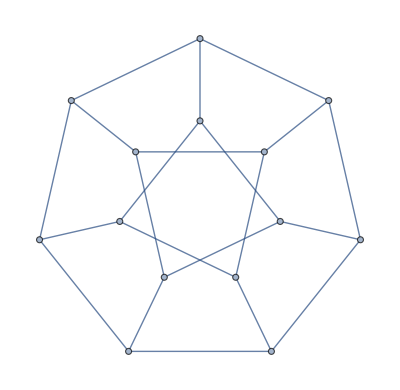
{graph,-Graphics-}

{Rasterize,Rasterize}

{HighlightGraph,HighlightGraph}

{FindVertexCover,FindVertexCover}

```mathematica
SHOW["graph=PetersenGraph[7,2];Rasterize[HighlightGraph[graph,FindVertexCover[graph]]]"];
```

```mathematica
SetOptions[ContourPlot3D,PlotPoints->30,Axes->False,Lighting->Automatic,ContourStyle->{RGBColor[1,.5,.5]},Mesh->None];
```

SetOptions::optnf: PlotStyle is not a known option for ContourPlot3D.

```mathematica
SHOW["ContourPlot3D[(2x^2+y^2+z^2-1)^3-(x^2*z^3)/10-y^2*z^3==0,{x,-1.4,1.4},{y,-1.4,1.4},{z,-1.4,1.4}]"];
```

-Graphics3D-

{ContourPlot3D,ContourPlot3D}

{x,x}

{y,y}

{z,z}